```mathematica
f[n_,l_,e_]:=√(n/l)e^-4.5 Log[n]^2 Log[1/e]
```

```mathematica
l[e_]:=n/.NSolve[f[n,1,e]/n==1,n][[3]]
```

```mathematica
Plot[{f[n,1,e]/n},{n,1.1,k},AspectRatio->1]
```

$Failed

```mathematica
l[.1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

9.73931×10^15

```mathematica
f[n_]:=Plot[x^2,{x,1,n}]
```

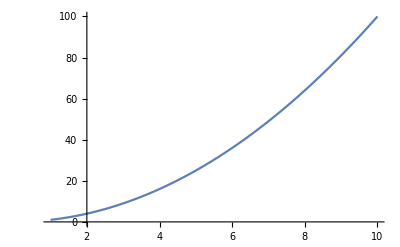

```mathematica
f[10]
```

```mathematica
l[e]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

Part::partw: Part 3 of NSolve[Log[1/e]\ Log[n]^2/e^4.5\ √n == 1, n] does not exist.

ReplaceAll::reps: {NSolve[Log[1/e]\ Log[n]^2/e^4.5\ √n == 1, n] ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

n/.NSolve[(Log[1/e] Log[n]^2)/(e^4.5 √n)==1,n]⟦3⟧

```mathematica
x/.NSolve[f[x,1,e]/x==1,x][[3]]
```

```mathematica
Hold
```

```mathematica
lineStyle={Thick,Red,Dashed};
Epilog->{Line[{{l[.1],0},{l[.1],1}}]}
f[e_]:=Plot[{f[n,1,e]/n,0},{n,1,(x/.NSolve[f[x,1,e]/x==1,x][[3]])*10},AspectRatio->Full,Epilog->{Line[{{x/.NSolve[f[x,1,e]/x==1,x][[3]],0},{x/.NSolve[f[x,1,e]/x==1,x][[3]],1}}],Text[(x/.NSolve[f[x,1,e]/x==1,x][[3]]),{(x/.NSolve[f[x,1,e]/x==1,x][[3]])*3,1}]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Epilog→{Line[{{9.73931×10^15,0},{9.73931×10^15,1}}]}

```mathematica
Label
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Epilog→{Line[{{9.73931×10^15,0},{9.73931×10^15,1}}]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

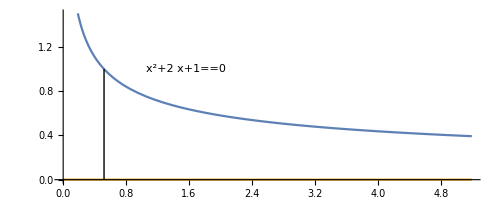

```mathematica
f[.4]
```

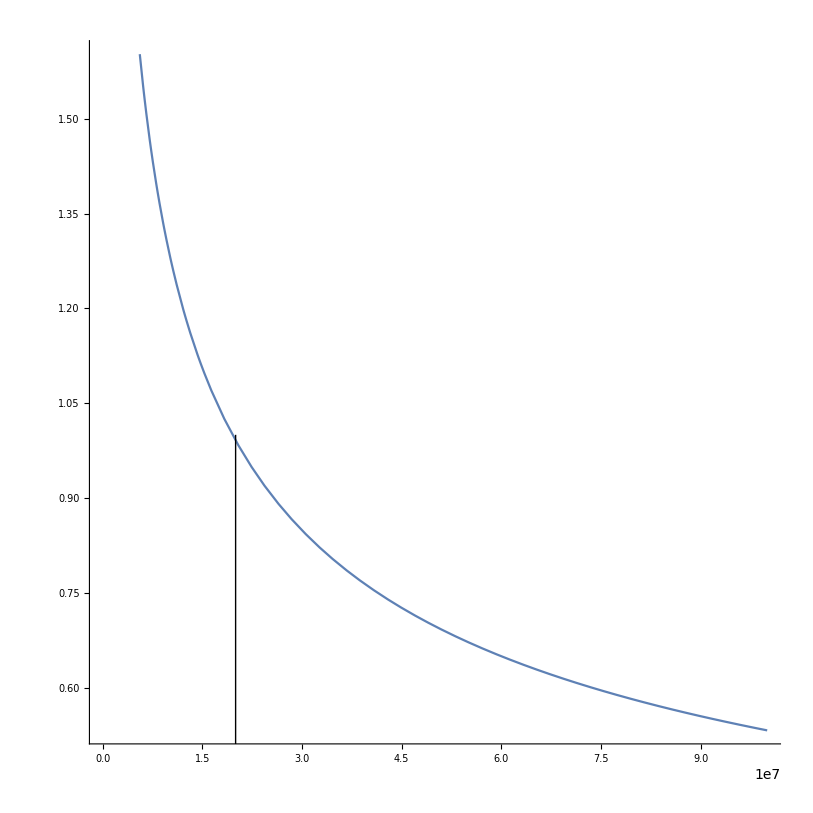

```mathematica
Show[p,Graphics[Line[{{20000000,0},{20000000,1}}]]]
```